Jakob Kastelic, 9/24/2018

## Wire grid reflectivity

#### Array of parallel wires (1D grid)

All the formulae in what follows taken from Wait, J.R. Appl. Sci. Res. (1955) 4: 393. https://doi.org/10.1007/BF02316501.

Units and constants:

```mathematica
$Assumptions:={Im[Ω]==0,Ω>0,m>0}
c=3 10^8 m/s;
GHz=10^9 s^-1;
μ0=4π 10^-7 H/m;
ϵ0=8.85 10^-12 s/Ω/m;
Z0=√(μ0/ϵ0);
mm=10^-3 m;
μm=10^-6 m;
cm=10^-2 m;
H=Ω s;
```

The grid dimensions are denoted by

```mathematica
a; (* radius of the wires *)
d; (* spacing between adjacent wires *)
```

Define the material properties for the wire (copper):

```mathematica
σ=1/(1.7 10^-6 Ω cm); (* conductivity of wires *)
μ1=μ0; (* permeability of wires *)
```

The fraction of transmitted power is

```mathematica
T[a_,d_,λ_]:=1-Abs[R[a,d,λ]]^2
```

The reflection coefficient is

```mathematica
R[a_,d_,λ_]:=-1/(1+2Zg[a,d,λ]/Z0)//FullSimplify;
```

The equivalent shunt impedance of the grid is given by [eqn 25]:

```mathematica
Zg[a_,d_,λ_]:=ⅈ Z0 d/λ(Log[d/(2π a)]+Fc[d,λ])+d Zi[a,λ];
```

The internal impedance of the wires is approximately [eqn 17]:

```mathematica
Zi[a_,λ_]:=√((μ1 2π c)/(2σ λ))(1+ⅈ)/(2π a)
```

The correction factor is [eqn 22]:

```mathematica
mMAX=100;
Fc[d_,λ_]:=∑_(m=1)^mMAX ((m^2-(d/λ)^2)^(-1/2)-1/m);
```

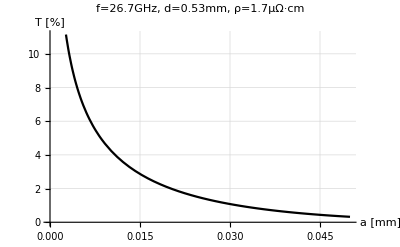

```mathematica
p1=Plot[
100T[a mm,0.53mm,c/(26.7GHz)],
{a,0,0.05},
AxesLabel->{"a [mm]","T [%]"},
PlotLabel->Style["f=26.7GHz, d=0.53mm, ρ=1.7μΩ·cm",14],
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
```

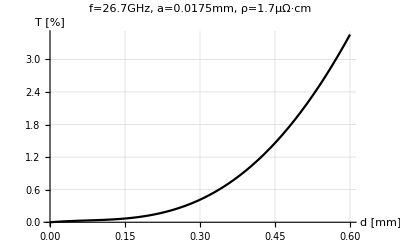

```mathematica
p2=Plot[
100T[0.0175 mm,d mm,c/(26.7GHz)],
{d,0,.6},
AxesLabel->{"d [mm]","T [%]"},
PlotLabel->Style["f=26.7GHz, a=0.0175mm, ρ=1.7μΩ·cm",14],
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
```

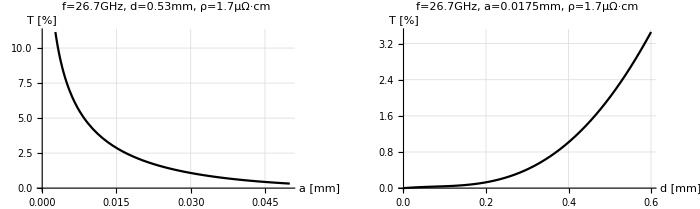

/home/jk/temp/thesis/figs/mathematica

```mathematica
pl=GraphicsGrid[{{p1,p2}},ImageSize->700]
SetDirectory[NotebookDirectory[]]
Export["wires.pdf",pl];
```